# Chapter 5 - Problem 5

Find the bound state energies of an electron entrapped in a rectangular potential well of width 4nm and depth 0.5 eV.

This problem is no longer a delta potential problem. That means that we will utilize both the PI and PP matrices to solve this problem.

```mathematica
Clear["Global`*"]
(* Constants *)
e = 1.60217 * 10^-19; (* 1 electron volt(ev) = e Joules *)
h = 6.62607004 * 10^-34 ;(* planck's constant *)
m = 9.10938 * 10^-31; (* effective mass of an electron *)
ℏ = h/(2*Pi);
alpha = Sqrt[(2*m*e)/ℏ^2] * 10^-9;
```

```mathematica
(*PI and PP matrices*)
PP[kx_,l_] = MatrixExp[-I * kx * l * PauliMatrix[3]];
PI [kL_, kR_] = MatrixExp[1/2 * Log[kL/kR] * (PauliMatrix[1] - IdentityMatrix[2])];
```

```mathematica
L = 4; (* the nm part is taken account for by alpha *)
V = -0.5 ;
kvacuum = alpha * Sqrt[en]; (* assuming that it came from vacuum*)
kwell = alpha * Sqrt[en - V];
```

```mathematica
M = PI[kvacuum, kwell].PP[kwell,L].PI[kwell, kvacuum];
```

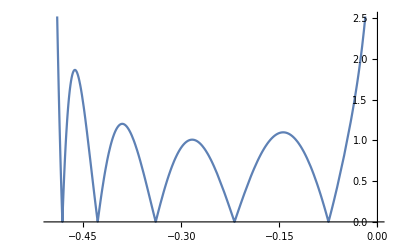

```mathematica
Plot[Abs[M[[1,1]]],{en, -0.5, 0}]
```

```mathematica
FindRoot[M[[1,1]],{en, -0.1}]
```

{en→-0.0748961+0. ⅈ}

```mathematica
FindRoot[M[[1,1]],{en, -0.2}]
```

{en→-0.218648+0. ⅈ}

```mathematica
FindRoot[M[[1,1]],{en, -0.34}]
```

{en→-0.339156+0. ⅈ}

```mathematica
FindRoot[M[[1,1]],{en, -0.42}]
```

{en→-0.427864+0. ⅈ}

```mathematica
FindRoot[M[[1,1]],{en, -0.48}]
```

{en→-0.48188+0. ⅈ}